# Quantum Gates & Quantum Circuits

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

```mathematica
<<Wolfram`QuantumFramework`
```

## Links

https://resources.wolframcloud.com/ExampleRepository/search/?i=quantum&sortBy=Relevance

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/tutorial/CircuitDiagram.html

## QuantumOperator

### Ejemplos y detalles

#### Ejemplo básico

```mathematica
op=QuantumOperator[{{1,-1},{1,1}}]
```

00-01+10+11

```mathematica
op["Eigenvalues"]
```

{1+ⅈ,1-ⅈ}

```mathematica
op["Eigenvectors"]
```

{{1/(√2),-ⅈ/(√2)},{1/(√2),ⅈ/(√2)}}

```mathematica
QuantumOperator[{{a,b},{c,d}},"PauliX"]
```

a𝓍_+𝓍_++b𝓍_+𝓍_−+c𝓍_−𝓍_++d𝓍_−𝓍_−

#### Transformación de bases

```mathematica
QuantumOperator[op,"X"]//TraditionalForm
```

𝓍_+𝓍_++𝓍_+𝓍_−-𝓍_−𝓍_++𝓍_−𝓍_−

```mathematica
%["Eigensystem"]
```

{{1+ⅈ,1-ⅈ},{{1/(√2),-ⅈ/(√2)},{1/(√2),ⅈ/(√2)}}}

#### Uso directo de matrices

```mathematica
mc=RandomComplex[{-1-I,1+I},{4,4}];
```

```mathematica
QuantumOperator[mc]
```

QuantumOperator[…]

### Circuitos nombrados

#### Matrices de Pauli

```mathematica
MatrixForm[QuantumOperator[#]["Matrix"]]&/@{"I","X","Y","Z"}
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

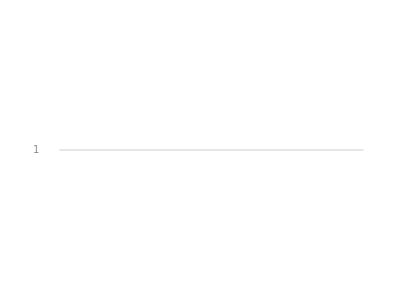
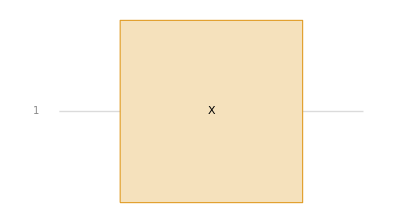
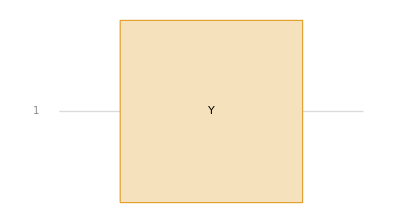
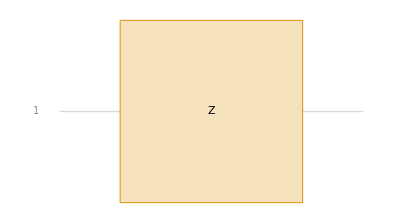

```mathematica
QuantumOperator[#]["CircuitDiagram",ImageSize->Tiny]&/@{"I","X","Y","Z"}
```

#### Rotaciones

```mathematica
MatrixForm[QuantumOperator[#]["Matrix"]]&/@{"RX"[θ1],"RY"[θ2],"RZ"[θ3]}
```

{(Cos[θ1/2] | -ⅈ Sin[θ1/2]
-ⅈ Sin[θ1/2] | Cos[θ1/2]),(Cos[θ2/2] | -Sin[θ2/2]
Sin[θ2/2] | Cos[θ2/2]),(ⅇ^(-(ⅈ θ3)/2) | 0
0 | ⅇ^((ⅈ θ3)/2))}

```mathematica
rxy=QuantumOperator[{"R",θ,"XY"}];
```

```mathematica
rxy["Matrix"]//MatrixForm
```

(Cos[θ/2] | 0 | 0 | -Sin[θ/2]
0 | Cos[θ/2] | Sin[θ/2] | 0
0 | -Sin[θ/2] | Cos[θ/2] | 0
Sin[θ/2] | 0 | 0 | Cos[θ/2])

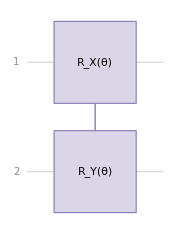

```mathematica
rxy["CircuitDiagram",ImageSize->Small]
```

#### Compuertas controladas

```mathematica
QuantumOperator["NOT"]["Formula"]
```

01+10

```mathematica
QuantumOperator["CNOT"]["Formula"]
```

0000+0101+1011+1110

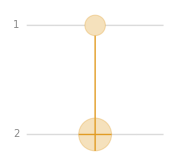

```mathematica
QuantumOperator[{"C","NOT",{1}}]["CircuitDiagram",ImageSize->Small]
```

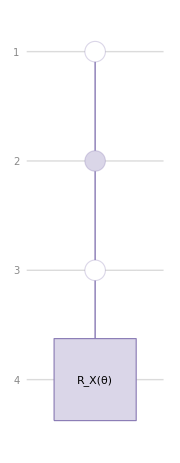

```mathematica
QuantumOperator[{"C","RX"[θ],{2},{1,3}}]["CircuitDiagram",ImageSize->Small]
```

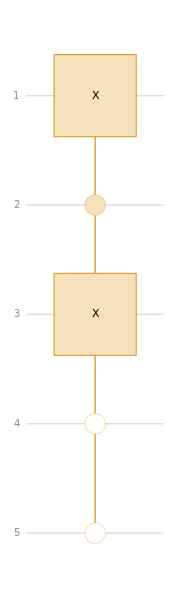

```mathematica
QuantumOperator[{"C","X"->{1,3},{2},{4,5}}]["CircuitDiagram",ImageSize->Small]
```

#### Gates U2 y U3

```mathematica
QuantumOperator[{"U2", ϕ ,λ}]
```

QuantumOperator[…]

```mathematica
QuantumOperator["U2"[ ϕ ,λ]]
```

QuantumOperator[…]

```mathematica
MatrixForm[%["Matrix"]]
```

(1/(√2) | -ⅇ^(ⅈ λ)/(√2)
ⅇ^(ⅈ ϕ)/(√2) | ⅇ^(ⅈ (λ+ϕ))/(√2))

```mathematica
QuantumOperator[{"U3",θ, ϕ ,λ}]
```

QuantumOperator[…]

```mathematica
QuantumOperator["U3"[θ, ϕ ,λ]]
```

QuantumOperator[…]

```mathematica
MatrixForm[%["Matrix"]]
```

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

#### Dimension y orden

```mathematica
h=QuantumOperator[{"Hadamard",2}]
```

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

```mathematica
hh=QuantumOperator["H"->{2}]
```

QuantumOperator[…]

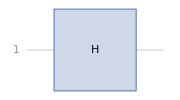
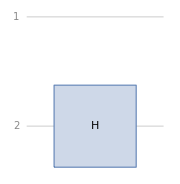

```mathematica
#["CircuitDiagram",ImageSize->Small]&/@{h,hh}//Row
```

```mathematica
QuantumOperator["H",{2,4,6}]
```

QuantumOperator[…]

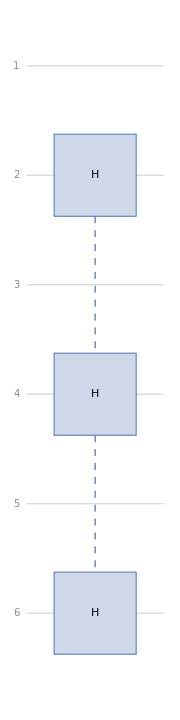

```mathematica
%["CircuitDiagram",ImageSize->Small]
```

```mathematica
QuantumOperator["H",2]
```

QuantumOperator[…]

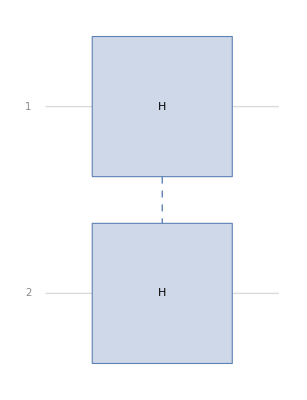

```mathematica
%["CircuitDiagram",ImageSize->Tiny]
```

```mathematica
%%==QuantumTensorProduct[h,h]
```

True

### Compatibilidad

#### Uso de Strings

Construcción de matrices de Pauli

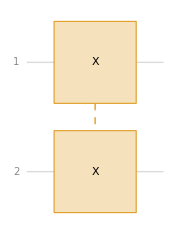

```mathematica
QuantumOperator["XX"]["CircuitDiagram",ImageSize->Small]
```

```mathematica
QuantumOperator["X",{1,2}]==QuantumOperator["X",2]==QuantumOperator["XX"]==QuantumOperator["X"->{1,2}]
```

True

Sumar matrices de Pauli

```mathematica
QuantumOperator["X"+"Y"]==QuantumOperator["X"]+QuantumOperator["Y"]
```

True

```mathematica
QuantumOperator[2"X"+θ"Y"]==2*QuantumOperator["X"]+θ*QuantumOperator["Y"]
```

True

#### Funciones de Wolfram Mathematica

```mathematica
Sqrt[QuantumOperator["X"]]
```

(1/2+ⅈ/2)00+(1/2-ⅈ/2)01+(1/2-ⅈ/2)10+(1/2+ⅈ/2)11

```mathematica
%==QuantumOperator["V"]==QuantumOperator["SX"]
```

True

```mathematica
Sqrt[QuantumOperator["NOT"]]==QuantumOperator["RootNOT"]
```

True

```mathematica
MatrixExp[-(ⅈ ϕ)/2 QuantumOperator["X"]]
```

QuantumOperator[…]

```mathematica
MatrixExp[-(ⅈ ϕ)/2 QuantumOperator["X"]]["Matrix"]//MatrixForm
```

(Cos[ϕ/2] | -ⅈ Sin[ϕ/2]
-ⅈ Sin[ϕ/2] | Cos[ϕ/2])

```mathematica
MatrixExp[-(ⅈ ϕ)/2 QuantumOperator["X"]]==QuantumOperator["RX"[ϕ]]
```

True

### Aplicación

#### Composición

(σ̂)_x=Ĥ(σ̂)_z Ĥ:

```mathematica
QuantumOperator[{"H","Z","H"}]
```

QuantumOperator[…]

```mathematica
%==QuantumOperator["X"]
```

True

#### QuantumState

```mathematica
QuantumOperator["X"][]
```

QuantumState[…]

```mathematica
QuantumOperator["X"][]==QuantumOperator["X"][QuantumState["0"]]
```

True

```mathematica
QuantumOperator["CNOT"][]
```

QuantumState[…]

#### Valor promedio

```mathematica
H=QuantumOperator[{{a,b},{c,d}}]
```

QuantumOperator[…]

Pure State

```mathematica
ϕ=QuantumState[{α,β}]
ϕ=SuperDagger[ϕ]
```

α0+β1

Conjugate[α]0+Conjugate[β]1

```mathematica
result=ϕ@H@ϕ
```

QuantumState[…]

```mathematica
result["Scalar"]//ComplexExpand
```

a α^2+b α β+c α β+d β^2

```mathematica
Simplify[result["Scalar"],{α,β}∈Reals]
```

a α^2+β (b α+c α+d β)

Mixed State

```mathematica
mat[r_]/;VectorQ[r]:=1/2(IdentityMatrix[2]+r.Table[PauliMatrix[i],{i,3}])
```

```mathematica
mat[{.1,.1,0}]
```

{{0.5+0. ⅈ,0.05-0.05 ⅈ},{0.05+0.05 ⅈ,0.5+0. ⅈ}}

```mathematica
mixed=QuantumState[mat[{.1,.1,.1}]]
```

QuantumState[…]

```mathematica
Tr[H[mixed["Operator"]]]
```

(0.55+0. ⅈ) a+(0.05+0.05 ⅈ) b+(0.05-0.05 ⅈ) c+(0.45+0. ⅈ) d

```mathematica
Tr[H["Matrix"].mixed["DensityMatrix"]]
```

(0.55+0. ⅈ) a+(0.05+0.05 ⅈ) b+(0.05-0.05 ⅈ) c+(0.45+0. ⅈ) d

Ejemplo completamente simbólico

```mathematica
Tr[H@QuantumState[mat[{α,β,γ}]]["Operator"]]
```

1/2 c (α-ⅈ β)+1/2 b (α+ⅈ β)+1/2 d (1-γ)+1/2 a (1+γ)

## QuantumCircuitOperator

### Composición

#### Ordenamiento

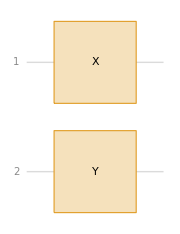

```mathematica
QuantumCircuitOperator[{QuantumOperator["X"],QuantumOperator["Y",{2}]}];
%["Diagram",ImageSize->Small]
```

```mathematica
%%==QuantumCircuitOperator[{"XY"}]==QuantumCircuitOperator[{"X"->{1},"Y"->{2}}]==QuantumCircuitOperator[{"X"->1,"Y"->2}]
```

True

```mathematica
qcorder=QuantumCircuitOperator[{QuantumOperator["X"],QuantumOperator["Y"],QuantumOperator["Z",{2}]}];
```

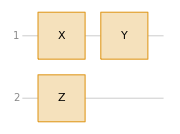

```mathematica
qcorder["Diagram",ImageSize->Small]
```

```mathematica
qcorder==QuantumCircuitOperator[{"XZ","Y"}]==QuantumCircuitOperator[{"X"->1,"Y"->1,"Z"->2}]
```

True

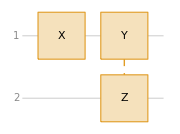

```mathematica
QuantumCircuitOperator[{"X"->1,"YZ"->2}]["Diagram",ImageSize->Small]
```

```mathematica
QuantumState[ⅇ^ϕ*"0"]==QuantumState["0"]
```

True

#### Inputs & Outputs

Circuito + Medida

```mathematica
QuantumState["Bell","Label"->"Bell"]
```

1/(√2)00+1/(√2)11

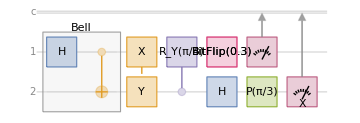

```mathematica
qc=QuantumCircuitOperator[{"Bell","XY",{"C","RY"[π/4]},"BitFlip"[.3],"H"->2,"P"[π/3]->2,{1},"M"["X"]->2}];
qc["Diagram"]
```

```mathematica
qc[]
```

QuantumMeasurement[…]

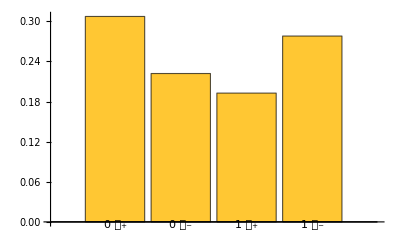

```mathematica
qc[]["ProbabilityPlot"]
```

```mathematica
qc[]["Mean"]
```

{0.470711,0.5}

Circuito + Estado resultante

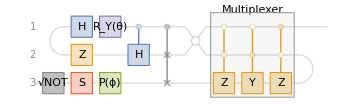

```mathematica
qc2=QuantumCircuitOperator[{"Cup","H","Z"->2,"RY"[θ],"RootNOT"->3,"S"->3,"P"[ϕ]->3,"CH","CSWAP","ZSpider"->{1,2}->{1,2},"Multiplexer"["Z","Y","Z"],"Cap"->{2,3}}];
qc2["Diagram"]
```

```mathematica
qc2[]
```

QuantumState[…]

```mathematica
qc2[]["Formula"]
```

(1/2+ⅈ/2) (Cos[θ/2]/(√2)-Sin[θ/2]/(√2))0+(1/2+ⅈ/2) ⅇ^(ⅈ ϕ) (-((Cos[θ/2]/(√2)-Sin[θ/2]/(√2))/(√2))+(Cos[θ/2]/(√2)+Sin[θ/2]/(√2))/(√2))1

### Circuitos nombrados

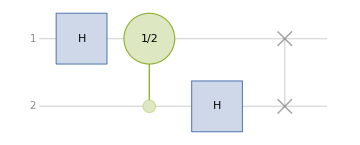

```mathematica
QuantumCircuitOperator["Fourier"]["Diagram"]
```

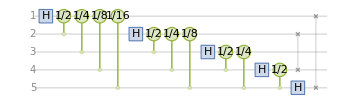

```mathematica
QuantumCircuitOperator["Fourier"[5]]["Diagram"]
```

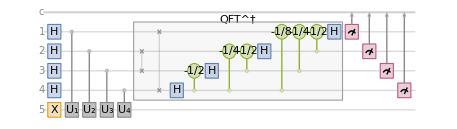

```mathematica
qpe=QuantumCircuitOperator["PhaseEstimation"];
qpe["Diagram"]
```

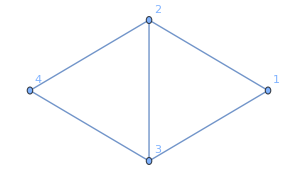

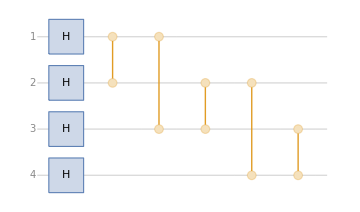

```mathematica
g=Graph[RandomGraph[{4,5}],VertexLabels->"Name"]
QuantumCircuitOperator["Graph"[g]]["Diagram"]
```

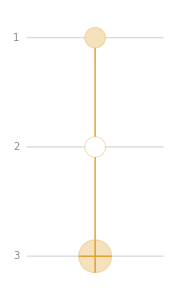

101

```mathematica
bo=QuantumCircuitOperator["BooleanOracle"[a&&!b]];
bo["Diagram",ImageSize->Small]
bo[QuantumState["100"]]["Formula"]
```

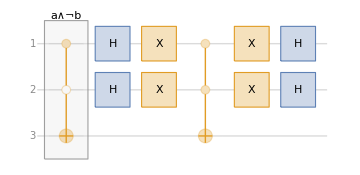

```mathematica
QuantumCircuitOperator["Grover"[a&&!b]]["Diagram"]
```

### Circuitos parametrizados

```mathematica
qc=QuantumCircuitOperator[{"RY"[θ],"RZ"[ϕ]},"Parameters"->{θ,ϕ}]
```

QuantumCircuitOperator[…]

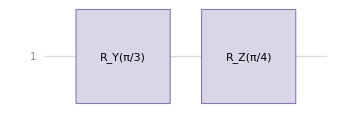

```mathematica
qc[<|ϕ->π/4,θ->π/3|>]["Diagram"]
```

```mathematica
qc[<|θ->π/3,ϕ->π/4|>]==qc[π/3,π/4]
```

True

```mathematica
qc[π/3,π/4][]==qc[][π/3,π/4]
```

True

## Ejercicios

Encuentra los eigenvalues, eigenvectors y representación diagonal de los operadores σ_x, σ_y, σ_z.

Del problema (1), expresalo en notación de Dirac usando la base {𝓊,𝒹} de la sesión anterior y despues en la base de sus eigenvectors.

Para ψ=√(2/3)𝓊+√(1/3)𝒹, calcula el valor esperado para σ_y.

Contruye los gates que realizan las siguientes transformaciones:

0->+=1/(√2)(0+1), 1->-+=1/(√2)(0-1)

+->+ⅈ=1/(√2)(0+ⅈ1), -->-ⅈ=1/(√2)(0-ⅈ1)

0->+ⅈ=1/(√2)(0+ⅈ1), 1->-ⅈ=1/(√2)(0-ⅈ1)

Contruye un gate que implemente las siguientes transformaciones

00->00, 01->01,10->11, 11->10

Explica paso por paso el Quantum Phase Estimation, puedes basarte en:

https://resources.wolframcloud.com/ExampleRepository/resources/Quantum-Phase-Estimation/

https://pennylane.ai/qml/demos/tutorial_qpe